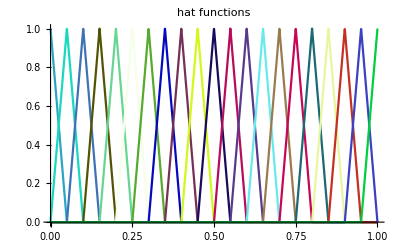

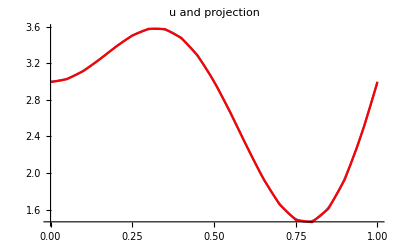

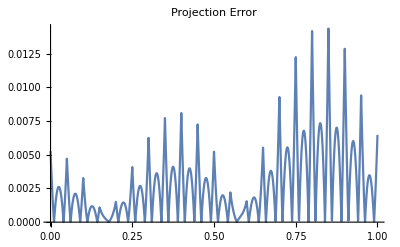

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.851547}. NIntegrate obtained 0.0000131 and 7.23425×10^-9 for the integral and error estimates.

The L^2-norm of the actual projection error is 0.00361939

The apriori upper bound of the error is 0.439738

```mathematica
globalMassMatrix[localMatrix_?MatrixQ,n_?IntegerQ]:=(
res=Table[Table[0,n],n];
rows=Length[localMatrix];
cols=Length[localMatrix[[1]]];

For[k=1,k≤n-rows+1,k++,
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
res[[k+i-1, k+j-1]]+=localMatrix[[i]][[j]];
];
];
];

res
)/; n≥Length[localMatrix]&&SquareMatrixQ[localMatrix]

globalLoadVector[u_,basis_?ListQ,points_?ListQ,blocksize_ :2 ]:=(
res=Table[0,Length[points]];

For[i=1,i≤Length[points]-blocksize+1,i++,
For[j=1,j≤blocksize,j++,
res[[i+j-1]]+=NIntegrate[u[x] basis[[i+j-1]][x],{x,points[[i]],points[[i+1]]}]
];
];

res
) /; IntegerQ[blocksize]

hat[i_?IntegerQ,points_?ListQ, x_?NumberQ]:=
Which[
i≥2&&i≤Length[points]-1,
Piecewise[{{(x-points⟦i-1⟧)/(points⟦i⟧-points⟦i-1⟧), points⟦i-1⟧≤x≤points⟦i⟧}, {(points⟦i+1⟧-x)/(points⟦i+1⟧-points⟦i⟧), points⟦i⟧≤x≤points⟦i+1⟧}, {0, True}}],
i==1,
Piecewise[{{(points⟦i+1⟧-x)/(points⟦i+1⟧-points⟦i⟧), points⟦i⟧≤x≤points⟦i+1⟧}, {0, True}}],
i==Length[points],
Piecewise[{{(x-points⟦i-1⟧)/(points⟦i⟧-points⟦i-1⟧), points⟦i-1⟧≤x≤points⟦i⟧}, {0, True}}]
]

(*Number of intervals*)
n=20;
minX = 0;
maxX = 1;
points = Table[minX + k (maxX-minX)/n,{k,0,n}];
colors = RandomColor@Length[points];
basis= Table[With[{i=k},hat[i,points,#1]&],{k,1,Length[points]}];

Show[
Table[
Plot[basis[[i]][x],{x,First[points],Last[points]}, PlotRange->All,PlotLegends->"Expressions", PlotStyle-> colors⟦i⟧],
{i,1,Length[points]}],
 PlotLabel-> "hat functions"]

u[x_]:=2 x Sin[2 Pi x]+3
h=(maxX-minX)/n;
massMatrix={
{h/3,h/6},
{h/6,h/3}
};

resMass = globalMassMatrix[massMatrix,Length[points]]; 
resMass//MatrixForm;
resLoad = globalLoadVector[u,basis,points, 2];
resLoad//MatrixForm;

projectionCoefficients = LinearSolve[resMass,resLoad];
projectionCoefficients // MatrixForm;
projection[basis_?ListQ,points_?ListQ,x_?NumberQ]:=∑_(i=1)^Length[points] projectionCoefficients[[i]] basis[[i]][x];
Show[{
Plot[u[x],{x,minX,maxX}, PlotRange->All],
Plot[projection[basis,points,x],{x,minX,maxX},PlotStyle->Red, PlotRange->All]
},
 PlotLabel-> "u and projection"]

projectionError[u_,basis_?ListQ,points_?ListQ,x_?NumberQ]:=u[x]-projection[basis,points,x]
Plot[Abs@projectionError[u,basis,points,x],{x,minX,maxX},
 PlotLabel-> "Projection Error"]

errorNorm[u_,basis_?ListQ,points_?ListQ]:=√NIntegrate[projectionError[u,basis,points,x]^2,{x,First[points],Last[points]}]
maxStep[points_?ListQ]:=Max@Differences[points]
L2Norm[u_,a_?NumberQ,b_?NumberQ]:=√NIntegrate[u[x]^2,{x,a,b}]
aprioriErrorEstimate[u_,points_?ListQ]:= √Length[points] L2Norm[u'',First[points],Last[points]] maxStep[points]^2 

StringForm["The L^2-norm of the actual projection error is ``",errorNorm[u,basis,points]]
StringForm["The apriori upper bound of the error is ``", aprioriErrorEstimate[u,points]]
```